```mathematica
$Assumptions=True;
Clear["Global`*"]
$Assumptions=True;
```

## Ackerman Kinematic

```mathematica
Manipulate[Plot[(ArcTan[Tan[x]/(1+0.5 WB$TW Tan[x])]-x)/x,{x,-0.3,0.3}],{WB$TW,0.5,1}]
```

## 1st State space Model

#### Parameters

```mathematica
Cf=3200;Cr=2600;Izz=4000;J1=0.1;J2=0.005;KK=30;b1=0.001;b2=1;b3=0.001;lf=1.4;lr=1.6;m=2000;vx=5;ξ=0.3;
```

#### Steering & Lateral System

(-10. | 0. | -300. | 300. | 0. | 0.
0. | -0.1 | 3000. | -603000. | 120000. | 168000.
1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 3. | -1.15 | -4.96
0. | 0. | 0. | 2.1 | 0.02 | -1.292)

(-0.641054+776.53 ⅈ
-0.641054-776.53 ⅈ
-5.00312+16.5387 ⅈ
-5.00312-16.5387 ⅈ
-0.626822+1.34414 ⅈ
-0.626822-1.34414 ⅈ)

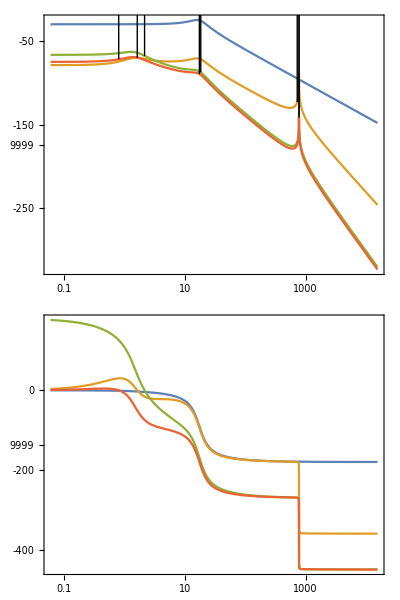

```mathematica
AA=({{-b2/J1, 0, -KK/J1, KK/J1, 0, 0}, {0, -b3/J2, KK/J2, -(KK+2Cf)/J2, 2 Cf/(J2 vx), 2(Cf lf)/(J2 vx)}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 0, (2Cf)/m, -2(Cf+Cr)/(m vx), 2(-Cf lf+Cr lr)/(m vx)-vx}, {0, 0, 0, (2Cf lf)/Izz, 2(-Cf lf+Cr lr)/(Izz vx), -2(Cf lf^2+Cr lr^2)/(Izz vx)}});BB=({{1/J1}, {0}, {0}, {0}, {0}, {0}});CC=({{0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});DD=({{0}, {0}, {0}, {0}});
SteeringSS=StateSpaceModel[{AA,BB,CC,DD}];
Print[AA//MatrixForm//N];Print[Eigenvalues[AA]//MatrixForm];
Print[BodePlot[SteeringSS,StabilityMargins->{True,True,True,True}]];
```

#### Modified S&L System

```mathematica
(*Manipulate[{Eigenvalues[({{-b2/J1-b1/J1, b1/J1, -KK/J1, KK/J1, 0, 0}, {b1/J2, -b3/J2-b1/J2, KK/J2, (-KK-2Cf ξ)/J2, 2(Cf ξ)/(J2 vx), 2(Cf lf ξ)/(J2 vx)}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 0, (2Cf)/m, -2(Cf+Cr)/(m vx), 2(-Cf lf+Cr lr)/(m vx)-vx}, {0, 0, 0, (2Cf lf)/Izz, 2(-Cf lf+Cr lr)/(Izz vx), -2(Cf lf^2+Cr lr^2)/(Izz vx)}})]//StandardForm},{KK,-10,10}]*)
Eigenvalues[({{-b2/J1-b1/J1, b1/J1, -KK/J1, KK/J1, 0, 0}, {b1/J2, -b3/J2-b1/J2, KK/J2, (-KK-2Cf ξ)/J2, 2(Cf ξ)/(J2 vx), 2(Cf lf ξ)/(J2 vx)}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 0, (2Cf)/m, -2(Cf+Cr)/(m vx), 2(-Cf lf+Cr lr)/(m vx)-vx}, {0, 0, 0, (2Cf lf)/Izz, 2(-Cf lf+Cr lr)/(Izz vx), -2(Cf lf^2+Cr lr^2)/(Izz vx)}})]//StandardForm
```

{-0.824049+624.502 ⅈ,-0.824049-624.502 ⅈ,-5.01514+16.4439 ⅈ,-5.01514-16.4439 ⅈ,-0.592209+1.31457 ⅈ,-0.592209-1.31457 ⅈ}

True

True

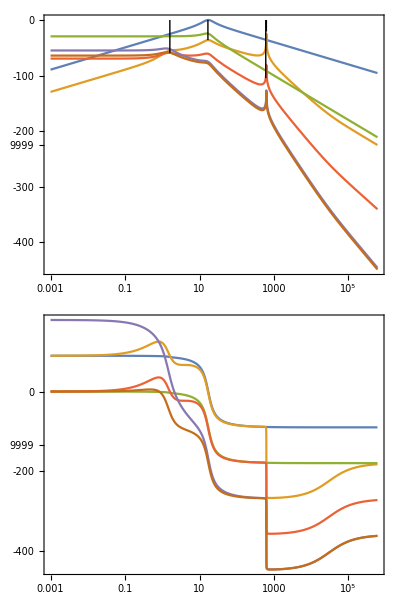

```mathematica
SteeringSS=StateSpaceModel[{({{-b2/J1-b1/J1, b1/J1, -KK/J1, KK/J1, 0, 0}, {b1/J2, -b3/J2-b1/J2, KK/J2, (-KK-2Cf ξ)/J2, 2(Cf ξ)/(J2 vx), 2(Cf lf ξ)/(J2 vx)}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 0, (2Cf)/m, -2(Cf+Cr)/(m vx), 2(-Cf lf+Cr lr)/(m vx)-vx}, {0, 0, 0, (2Cf lf)/Izz, 2(-Cf lf+Cr lr)/(Izz vx), -2(Cf lf^2+Cr lr^2)/(Izz vx)}}),({{1/J1}, {0}, {0}, {0}, {0}, {0}}),IdentityMatrix[6],({{0, 0, 0, 0, 0, 0}})ᵀ}];
Print[ControllableModelQ[SteeringSS]]
Print[ObservableModelQ[SteeringSS]]
BodePlot[SteeringSS,StabilityMargins->{True,True,True,True}]
```

#### Lateral System

```mathematica
Eigenvalues[({{-2(Cf+Cr)/(m vx), 2(-Cf lf+Cr lr)/(m vx)-vx}, {2(-Cf lf+Cr lr)/(Izz vx), -2(Cf lf^2+Cr lr^2)/(Izz vx)}})]//MatrixForm
```

(-1.221+0.306853 ⅈ
-1.221-0.306853 ⅈ)

## Lateral-Steering System

clear

```mathematica
$Assumptions = True;
Clear["Global`*"]
```

#### external forces

```mathematica
(*drag force by aerodynamics*)
Fdx[t_]:=0;
Fdy[t_]:=0;
Fdz[t_]:=0;
Mdx[t_]:=0;
Mdy[t_]:=0;
Mdz[t_]:=0;
Fxext[t_]:=Fdx[t];
Fyext[t_]:=Fdy[t];
Fzext[t_]:=Fdz[t];
Mxext[t_]:=Mdx[t];Myext[t_]:=Mdy[t];Mzext[t_]:=Mdz[t];
```

#### external longitudinal velocity

```mathematica
Fxft[t_]:=0;
Fxrt[t_]:=0;
Fyft[t_]:=-Cyfl αf[t] (*μfl*) (Fzf[t]/Fznom);
Fyrt[t_]:=-Cyrl αr[t] (*μrl*) (Fzr[t]/Fznom);
```

#### weight and load transfer by varying the effective friction parameters

```mathematica
(*Fzf[t_]:=1/(a+b)(b m g-(ddx[t]-dy[t] dψ[t]) m h+h Fxext[t]+b Fzext[t]-Myext[t]);
Fzr[t_]:=1/(a+b)(a m g+(ddx[t]-dy[t] dψ[t]) m h-h Fxext[t]+a Fzext[t]+Myext[t]);*)
Fzf[t_]:=Fznom;Fzr[t_]:=Fznom;
```

#### slip angles

```mathematica
αf[t_]:=(dy[t]+a dψ[t])/dx[t]-δf[t];
αr[t_]:=(dy[t]-b dψ[t])/dx[t];
```

#### steering angles of the tire(wheel)

```mathematica
(*Fxf[t_]:=Fxft[t] Cos[δf[t]]-Fyft[t] Sin[δf[t]];
Fyf[t_]:=Fxft[t] Sin[δf[t]]+Fyft[t] Cos[δf[t]];*)
Fxf[t_]:=Fxft[t];
Fyf[t_]:=Fyft[t];
Fxr[t_]:=Fxrt[t];
Fyr[t_]:=Fyrt[t];
```

#### DYNAMICS

```mathematica
ddx[t_]:=0;dx[t_]:=vx;
sol=Solve[{ddy[t]==-dx[t] dψ[t]+1/m(Fyf[t]+Fyr[t]+Fyext[t]),
ddψ[t]==1/Izz(a Fyf[t]-b Fyr[t]+Mzext[t])},{ddy[t],ddψ[t]}];
sol$ddy[t_]:=Evaluate[sol[[1,1,2]]];
sol$ddψ[t_]:=Evaluate[sol[[1,2,2]]];
Print[ddy[t],"=",sol$ddy[t](*//Simplify*)~Collect~{dy[t],dψ[t],δf[t]}//StandardForm];
Print[ddψ[t],"=",sol$ddψ[t](*//Simplify*)~Collect~{dy[t],dψ[t],δf[t]}//StandardForm];
```

ddy[t]=((-Cyfl-Cyrl) dy[t])/(m vx)+((-a Cyfl+b Cyrl-m vx^2) dψ[t])/(m vx)+(Cyfl δf[t])/m

ddψ[t]=((-a Cyfl+b Cyrl) dy[t])/(Izz vx)+((-a^2 Cyfl-b^2 Cyrl) dψ[t])/(Izz vx)+(a Cyfl δf[t])/Izz